# Intro to Mathematica

## What makes Mathematica unique?

Mathematica is built from the ground up to do SYMBOLIC math.  Programs like Matlab and R work with equations, of course, but they are best suited to NUMERIC computation.  Mathematica really helps you do MATH (e.g., like algebra, trig, and calculus), as opposed to only doing CALCULATIONS (i.e., manipulating and combining numbers).

## Input and formatting in Mathematica, part 1

This file is a type of document called a “notebook”, which is the basic file format in Mathematica.  The file has a proprietary (i.e., Mathematica-specific) format; it is not a plain text file.  That means it will only display properly when viewed in Mathematica.  That might seem undesireable to you, but  Mathematica is super badass, so we will live with that one flaw (which isn’t really a flaw).
The benefit here is that we can EASILY create documents are are “computable” and human readible at the same time!  Yay!

Note the left-most square bracket (“]”) in the right hand margin (over there -->)
That demarcates a “cell”, which is the basic unit of input in mathematica
Cells that are formatted as mathematical “input” can be evaluated.  When you press “shift-return” on your keyboard, ALL the contents of the current cell (where your cursor is) will be evaluated.  When you have a vertical cursor, you are inside a cell.  When you have a horizontal line and cursor, you are in between cells (and if you start typing, it will insert a new cell at that spot).

Looking around this notebook, you’ll see cells with a variety of formats.  Again, that is part of what makes it easy to make files that are simultaneously computable and human readable.  We are primarily concerned with using Mathematica to help us do math. Actual math will appear in cells that have the format of “input” or “output” (labeled “In” and “Out” in the left margin once evaluated).  More on this below.

Any cell can contain one or multiple expressions:

```mathematica
"here is a cell with one comment and one mathematical expression. The following cell has two mathematical expressions.  The semicolon outside the double quotes will suppress this comment from being printed to the screen.";
y=3*x+5
```

5+3 x

```mathematica
w=5*y
z=y^2
```

5 (5+3 x)

(5+3 x)^2

Note that Mathematica “remembers” what you have previously evaluated, so when I used “y” in the second line, it automatically substituted the assigned value of y

As in many languages, “=” is the “assignment operator.”  Mathematica is very nice about how you use this and what can be “assigned” to a variable.  You can assign a value, a symbolic variable, an expression of mixed components, a data array, a list of rules, a graphical object, and more...

```mathematica
a=1
a=x
a=x+1
a={1,2,3,4,z}
```

1

x

1+x

{1,2,3,4,(5+3 x)^2}

Each time I type and evaluate a new assignment to the variable “a”, Mathematica upates what is stored in that variable.  It will remember that value for as long as I keep this “notebook” open.

## Evaluting Input

I have been talking about “evaluating” input without saying much about how you get Mathematica to DO that evaluation.   There is really only one subtle thing here.  On most computer operating systems, if you press “return” or whatever the carriage return key is labeled (sometimes labeled “enter”), you get a carriage return (i.e., a line break).  This is handy because it allows you to put multiple lines of expressions in the same cell.  However, to have Mathematica evaluate your input, you need to press “Shift-Return”.  If you have a numeric keypad on the far right of your keyboard with an “Enter” key, you can also just press that Enter key on most operating systems when you want Mathematica to evaluate.

## Input and formatting in Mathematica, part 2

```mathematica
the section title above ("Input and formatting in Mathematica, part 2")was made with a special formatting selection for that cell.  Stuff you type is interpreted as mathematical "input" by default, so, since I did not specify any kind of formatting for THIS current cell, mathematica thinks this sentence is a set of variables and does not like the  non-mathematical punctuation marks like the commas.  Hence it can not evaluate this if you tell it to, but rather gives an error message, which you can see by clicking on the little plus sign to the right after trying to evaluate this cell.
```

```mathematica
Mathematica can handle expressions like this one though
```

can expressions handle like Mathematica one this though

```mathematica
notice it alphabetizes the order of variables in its output
```

alphabetizes in it its notice of order output the variables

```mathematica
notice also that two or more characters together with no spaces between are treated as one variable
```

also are as between characters more no notice one or spaces that together treated two variable with

```mathematica
so gfe is treated differently than g f e because single space is interpreted as multiplication
```

as because differently e f g gfe interpreted is^2 multiplication single so space than treated

```mathematica
Mathematica can treat A sentence like this one as math because a variable can be one letter long or a bunch of letters long and a blank space between variables is interpreted as multiplication
```

{A and as^2 be because between blank bunch can^2 interpreted is letter letters like long^2 math Mathematica multiplication of one^2 or sentence space this treat variable variables,8 A and as^2 be because between blank bunch can^2 interpreted is letter letters like long^2 math Mathematica multiplication of one^2 or sentence space this treat variable variables,27 A and as^2 be because between blank bunch can^2 interpreted is letter letters like long^2 math Mathematica multiplication of one^2 or sentence space this treat variable variables,64 A and as^2 be because between blank bunch can^2 interpreted is letter letters like long^2 math Mathematica multiplication of one^2 or sentence space this treat variable variables,A and as^2 be because between blank bunch can^2 interpreted is letter letters like long^2 math Mathematica multiplication of one^2 or sentence space this treat variable variables (5+3 x)^6}

Can you figure out why the last expression was displayed as it was in the output?

```mathematica
Mathematica also automatically substitutes and groups factors together when it can
```

also and automatically can factors groups it Mathematica substitutes together when

Does it make sense to you that Mathematica wrote “as-squared,” “it-squared”, etc. in the last two sets of output?  How about why “a” did not appear in the output and why “A” was not treated the same as “a”?
OK, these examples might seem kind of silly, but they really do illustrate how Mathematica treats the input YOU give it.  Remember, this is piece of computer software.  It does not think per se (at least not yet, though Mathematica is getting really close to that).  It does what YOU tell it to do, no more and no less.  When you give it “input”, by default it interprets that input as a mathematical expression.

## Functions and Syntax

Like all software for doing quantitative operations, a big part of what makes Mathematica useful and powerful is that it has a HUGE number of built in functions available for use that cover the common and even not so common things that people like us tend to do.  Like all such software, Mathematica also has a syntax (i.e., set of “grammatical rules”) for how functions are used.  The basic syntax usuall goes something like this:
FunctionName[argument1, argument2, ..., optionalArgument1, ...]
There are some important details here:
1. The square braces.  In Mathematica, these are used for functions.  NOT parentheses.  NOT curly braces (more on those below).
2.  Arguments.  An argument is an input(s) to a function.  Different functions take different numbers of arguments and different formats of arguments.  Parentheses and curly braces may often help format arguments.
3.  Commas separate arguments.  That’s how Mathematica knows where one argument stops and the next begins.
4.  Optional arguments aren’t necessary (as the name implies) but can change the behavior of the function in various useful ways
Let’s look at an example by first defining a new variable:

```mathematica
b=w^2-w
```

-5 (5+3 x)+25 (5+3 x)^2

The output is a messy expression, so let’s use a built-in function to simplify it, shall we?

```mathematica
FullSimplify[b]
```

15 (5+3 x) (8+5 x)

OK, so let’s break down what we just did.  We used a FUNCTION named “FullSimplify” to perform an operation on the expression that is stored in the variable b.  b was the “argument” we passed to the function.  Just for kicks, let’s see what b looks like now:

```mathematica
b
```

-5 (5+3 x)+25 (5+3 x)^2

Huh?  Note that b appears NOT simplified.  Why?  Because we simplified the expression stored in b, but did not re-assign it.  To really make the simplification take effect, we need to re-assign the variable:

```mathematica
b=FullSimplify[b]
```

15 (5+3 x) (8+5 x)

```mathematica
b
```

15 (5+3 x) (8+5 x)

See why that works now?  If not, give it some thought.

## Basic Plotting

One of the most useful features of Mathematica for working with biological models is how easy it is to visualize your equations using the rich library of plotting functions that Mathematica has.  Let’s define and work with a simple linear equation:

```mathematica
Clear[b];
y=4*x^b
```

4 x^b

Note that to re-use the variable b for a new purpose here, we had to clear it first, which we did with a function named “Clear”.
OK, so let’s plot y as a function of x, as x ranges from zero to 10.

```mathematica
Plot[y,{x,0,10}]
```

-Graphics-

Why is the plot blank? Because b is still just a symbol, so the numeric value of y can not be computed.  We have several ways to get around this, all of which are useful in different contexts.

### So, let’s look at four ways to play with equations that have more than one independent variable.

### A. Brute force: assign a numeric value to b

Suppose we do the following

```mathematica
b=-2
```

-2

Note what we get now for the value assigned to y:

```mathematica
y
```

4/x^2

Now our plot will work:

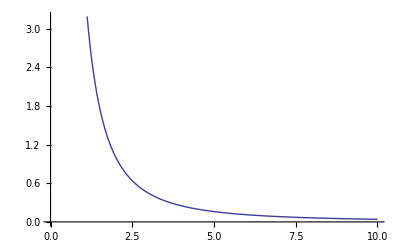

```mathematica
Plot[y,{x,0,10}]
```

#### A.1. Breaking down the Plot[...] function’s syntax

OK, now we need one more little bit on syntax.  Let’s look at how we wrote the Plot function above:
Plot[y,{x,0,10}]
Again, we have a general form here:  FunctionName[argument1, argument2], though that might not look so obvious.  argument1 is easy, that’s “y”.  argument2 however looks like three arguments until we note the curly braces (I said we would come back to those, right?).  Curly braces in Mathematica are used to enclose LISTS or ARRAYS of things.  In this case, we have a list that tells the Plot function three things: (i) the name of the independent variable, x, (ii) the minimum value x takes, and (iii) the maximum value x takes.  How does Plot “know” how to intrepret those three things in that way?  That’s in how the creators of Mathematica wrote the Plot function.  Argument2 has to have this form.  How would you know that?  That’s part of learning the language.  Let’s try something different and see what happens:

```mathematica
Plot[y,x,0,10]
```

Plot::nonopt: Options expected (instead of 10) beyond position 3 in Plot[y, x, 0, 10]. An option must be a rule or a list of rules.

Plot[y,x,0,10]

Oh, so you weren’t “expecting” that, eh, Mathematica?  Why not?  Because it is not a person who tries to anticipate and fix errors; it is a piece of software that does EXACTLY what you tell it to do.  (Oh yes, I am aware of Mathematica’s new “freeform input” functionality, but we’ll talk about that later...).

#### A.2. Brute force assignment of a value to b works, but can we do better?

Our method for getting a plot of y worked, but wasn’t very elegant, because we have lost some generality in our ability to work with y.  Can we do better?  Yes, as the following three methods illustrate.

### B. Alternative Method #1: Use a substitution that does not change the value assigned to b

```mathematica
Clear[b]
y
```

4 x^b

OK, now we’ve got good old b back to being a symbolic variable, and Mathematica also puts it back into the expression for y.  That is cool.  Let’s introduce a new operation: a substitution rule, which takes the form:
expression / .variable->value:

```mathematica
Plot[(y/.b->-2),{x,0,10}]
```

-Graphics-

The cool thing here is that we haven’t lost any generality, yet we can look at a plot for a specific case.  In fact, we could look at a bunch of cases if we wanted to:

4/x^2

4

4 x^2

4 x^4

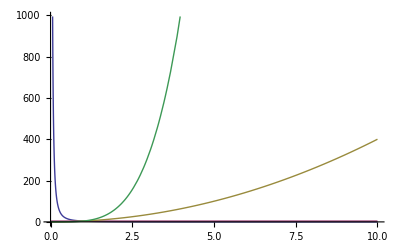

```mathematica
y1=y/.b->-2
y2=y/.b->0
y3=y/.b->2
y4=y/.b->4
Plot[{y1,y2,y3,y4},{x,0,10}]
```

Note that b is unchanged by these operations:

```mathematica
b
```

b

### C. Alternative Method #2: “Manipulate”

“Manipulate” is a super cool function in Mathematica.  Check it out.  The syntax might seem funky here, so pay careful attention to where braces open and close, and where commas, etc. appear.  Note that the “Plot[...]” function is nested inside the “Manipulate[...]” function

```mathematica
Manipulate[Plot[4*x^b,{x,0,10}],{b,-10,10}]
"Use the slider that appears in the box to literally manipulate b and see how the value of y=4 x^b changes.  Click the tiny plus sign next to the slider to see more options";
```

Note: one limitation of “Manipulate” seems to be that you have to put in the actual expression (4*x^b) rather than being able to simply write “y” as we do with other functions.  There are more elegant workarounds for Manipulate than this, but we won’t worry about them just yet.

### D. Alternative Method #3: 3-D plots

Plot3D is another great plotting function for when you want to vary two variables simultaneously.  Again, note the use of braces, commas, and where the dependent and indepenent variables appear as arguments.

```mathematica
Plot3D[y,{x,0,10},{b,-1,1}]
```

-Graphics3D-

I’ve been using Mathematica for over a decade, and I am still super impressed by how little effort (on my part) it takes to generate something as complex as a 3-D surface plot.  Don’t get me wrong, I love MATLAB, but generating this kind of plot in MATLAB is a serious pain compared to the one-line entry above.